```mathematica
Quit[]
```

```mathematica
Ready
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

# Plots for review

## Definitions

```mathematica
P[m_,n_,x_]=((1+x)/(1-x))^(m/2)*1/Gamma[1-m]*Hypergeometric2F1[n+1,-n,1-m,1/2(1-x)];
```

```mathematica
Q[m_,n_,x_]=Pi/2/Sin[Pi*m]*(Cos[Pi*m]*((1+x)/(1-x))^(m/2)*1/Gamma[1-m]*Hypergeometric2F1[n+1,-n,1-m,1/2(1-x)]-Gamma[n+m+1]/Gamma[n-m+1]*((1-x)/(1+x))^(m/2)*1/Gamma[1+m]*Hypergeometric2F1[n+1,-n,1+m,1/2(1-x)]);
```

```mathematica
QT[m_,n_,x_]=Sqrt[Pi]/2^(n+1)/x^(1+n+m)*(x^2-1)^(m/2)*1/Gamma[n+3/2]*Hypergeometric2F1[1/2*n+1/2*m+1,1/2*n+1/2*m+1/2,n+3/2,1/x^2];
```

```mathematica
y=1-(1-cs^2(u-v)^2)/(2cs^2u*v);
```

```mathematica
F1=(4v^2-(1-u^2+v^2)^2)^2/(4u^2v^2)^2;
```

```mathematica
F2=Abs[1-y^2]^b;
```

```mathematica
F3=4^(2b)/3/cs^4*Gamma[b+3/2]^4*(b+2)^2/(2b+3)^2*(1+b)^(-2(1+b));
```

```mathematica
T[u_,v_,b_,cs_]=F1*F2*F3*((P[-b,b,y]+(b+2)/(1+b)*P[-b,b+2,y])^2HeavisideTheta[cs(u+v)-1]+4/Pi^2(Q[-b,b,y]+(b+2)/(1+b)*Q[-b,b+2,y])^2HeavisideTheta[cs(u+v)-1]+4/Pi^2(QT[-b,b,-y]+2(b+2)/(1+b)*QT[-b,b+2,-y])^2HeavisideTheta[1-cs(u+v)]);
```

## Plots dirac delta

```mathematica
ΩGWs[k_,b_,cs_,kpkrh_]=Re[k^(-2-2b)*kpkrh^(-2b)*T[1/k,1/k,b,cs]];
```

```mathematica
bb[ww_]=(1-3ww)/(1+3ww);w[b_]=1/3(1-b)/(1+b);
```

```mathematica
DlnΩGWs[k_,b_,cs_,kpkrh_]=Re[k*D[k^(-2-2b)*kpkrh^(-2b)*T[1/k,1/k,b,cs],k]]/ΩGWs[k,b,cs,kpkrh]/.Abs'[x_]->0;
```

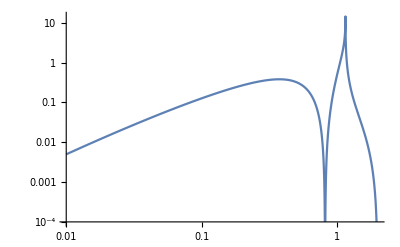

```mathematica
LogLogPlot[ΩGWs[k,0.0001,Sqrt[w[0.0001]],1],{k,10^(-2),2}]
```

```mathematica
krange=10^Range[Log10[10^(-2)],Log10[2],0.001];
```

```mathematica
OMGW13=Table[{Log10[k],Log10[ΩGWs[k,0.0001,Sqrt[w[0.0001]],10^(2)]]},{k,krange}];
```

```mathematica
OMGW13cs1=Table[{Log10[k],Log10[ΩGWs[k,0.0001,1,10^(2)]]},{k,krange}];
```

```mathematica
OMGW09=Table[{Log10[k],Log10[ΩGWs[k,-0.46,Sqrt[0.46],10^(2)]]},{k,krange}];
```

```mathematica
OMGW09der=Table[{k,DlnΩGWs[k,-0.46,Sqrt[0.46],10^(2)]},{k,krange}]//N;
```

```mathematica
OMGW09cs1=Table[{Log10[k],Log10[ΩGWs[k,-0.46,1,10^(2)]]},{k,krange}];
```

```mathematica
OMGW19=Table[{Log10[k],Log10[ΩGWs[k,1/2,Sqrt[w[1/2]],10^(2)]]},{k,krange}];
```

```mathematica
OMGW19cs1=Table[{Log10[k],Log10[ΩGWs[k,1/2,1,10^(2)]]},{k,krange}];
```

```mathematica
OMGW19der=Table[{k,DlnΩGWs[k,1/2,Sqrt[w[1/2]],10^(2)]},{k,krange}]//N;
```

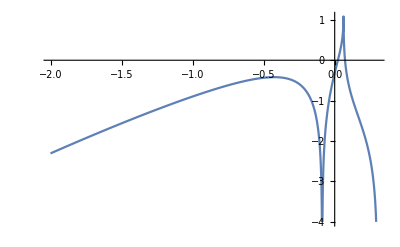

```mathematica
ListLinePlot[OMGW13]
```

```mathematica
Export["data/OMGW19.dat",OMGW19];Export["data/OMGW19der.dat",OMGW19der];
```

```mathematica
Export["data/OMGW09.dat",OMGW09];Export["data/OMGW09der.dat",OMGW09der];
```

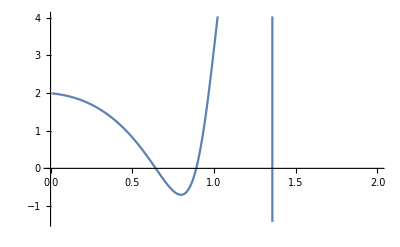

```mathematica
ListLinePlot[OMGW09der]
```

## Plots log-normal

```mathematica
3/4/10^2//N
```

0.0075

```mathematica
ΩGWLN[k_,b_,cs_,kpkrh_,Δ_]=Erf[1/Δ*ArcSinh[k/2]]*ΩGWs[k,b,cs,kpkrh];
```

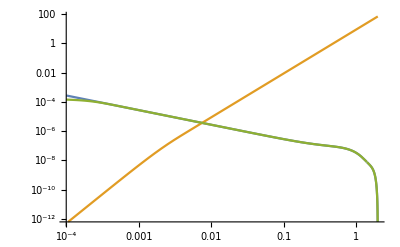

```mathematica
LogLogPlot[{ΩGWs[k,3/2,1,10^2],Erf[1/10^(-3)*ArcSinh[k/2]]*ΩGWs[3/4/10^2,3/2,1,10^2]*(k/(3/4/10^2))^3,ΩGWLN[k,3/2,1,10^2,10^(-4)]},{k,10^(-4),2}]
```

```mathematica
krange1=10^Range[Log10[3/4/10^2],Log10[2],0.001];krange2=10^Range[Log10[10^(-4)],Log10[3/4/10^2],0.001];
```

```mathematica
krange3=Join[krange2,krange1];
```

```mathematica
kN3=Length[krange3];
```

```mathematica
OMGWtest1=Table[ΩGWLN[k,3/2,1,10^2,10^(-5)],{k,krange1}];
OMGWtest2=Table[Erf[1/10^(-5)*ArcSinh[k/2]]*ΩGWs[3/4/10^2,3/2,1,10^2]*(k/(3/4/10^2))^3,{k,krange2}];
```

```mathematica
OMGWtest=Join[OMGWtest2,OMGWtest1];
```

```mathematica
OMGWdelta=Table[{Log10[krange3[[i]]],Log10[OMGWtest[[i]]]},{i,1,kN3}];
```

```mathematica
OMGWtest1m3=Table[ΩGWLN[k,3/2,1,10^2,10^(-3)],{k,krange1}];
OMGWtest2m3=Table[Erf[1/10^(-3)*ArcSinh[k/2]]*ΩGWs[3/4/10^2,3/2,1,10^2]*(k/(3/4/10^2))^3,{k,krange2}];
```

```mathematica
OMGWtestm3=Join[OMGWtest2m3,OMGWtest1m3];
```

```mathematica
OMGWm3=Table[{Log10[krange3[[i]]],Log10[OMGWtestm3[[i]]]},{i,1,kN3}];
```

```mathematica
OMGWtest1m1=Table[ΩGWLN[k,3/2,1,10^2,10^(-1)],{k,krange1}];
OMGWtest2m1=Table[Erf[1/10^(-1)*ArcSinh[k/2]]*ΩGWs[3/4/10^2,3/2,1,10^2]*(k/(3/4/10^2))^3,{k,krange2}];
```

```mathematica
OMGWtestm1=Join[OMGWtest2m1,OMGWtest1m1];
```

```mathematica
OMGWm1=Table[{Log10[krange3[[i]]],Log10[OMGWtestm1[[i]]]},{i,1,kN3}];
```

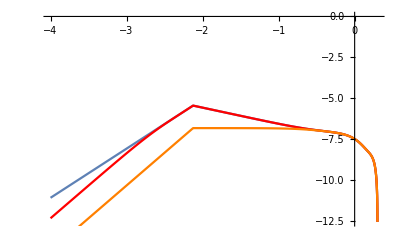

```mathematica
Show[ListLinePlot[OMGWdelta],ListLinePlot[OMGWm3,PlotStyle->Red],ListLinePlot[OMGWm1,PlotStyle->Orange]]
```

```mathematica
Export["/Users/guillemdomenech/Dropbox/ReviewSIGWB/OMGWdelta.dat",OMGWdelta];
```

```mathematica
Export["/Users/guillemdomenech/Dropbox/ReviewSIGWB/OMGWm3.dat",OMGWm3];
```

```mathematica
Export["/Users/guillemdomenech/Dropbox/ReviewSIGWB/OMGWm1.dat",OMGWm1];
```

```mathematica
w[3/2]
```

-1/15